# GH, SHEL and OIF Shifts: Single Interface M. T. Lusk Last Edited: November 10, 2016

-Graphics-

## Plotting Tools

```mathematica
Clear[font,coloredfont];
font[name_,size_]:=Style[name,FontFamily->"Tahoma",FontSize->size,Bold]

coloredfont[name_,size_,color_]:=Style[name,FontFamily->"Helvetica",FontSize->size,Bold, color]
```

## Theory

### Basic Theory of Modal Representation of the E-Field

References:

[1] An angular spectrum representation approach to the Goos-Hanchen shift, M. McGuirk and C. K. Carniglia, J.Opt. Soc. Am. Vol 67(1) p 103 1977 [Spectral_Decomposition_McGuirk_JOSA_1977.pdf]

[2] Optical Coherence and Quantum Optics, Mandel and Wolf [Quantum_Optics_Mandel_Wolf.pdf]

McGuirk gives the key result and some hints about the proof, while Mandel gives a step-by-step detailed proof. See Mandel p111 Eq 3.2-12. This is the derivation repeated below.

Consider a beam characterized by

E⃗[r⃗,t]=E[r⃗] f ⅇ^(ⅈ(k_0·r- ω t))

Here f is the fixed polarization of the beam. This is a monchromatic beam since there is only 1 temporal frequency, ω. Since k_0=k_0 κ_0, we immediately have that k_0=ω/c. The beam can be decomposed into plane waves via a Fourier transform, but the magnitude of each wave vector must be k_0 because both the speed and temporal frequency are fixed. Thus, the E-field can be described in terms of a spectrum of mono-length wave vectors:

k=k_0 κ.

Suppose our incident beam, traveling with central wave vector, k_0, makes an angle of θ with a planar interface with unit normal, n̂.

It will be convenient to define the beam frame, which is fixed once θ is prescribed. Let u_3 be the unit vector along the beam axis. Then

u_2= n×u_3

u_1= u_2×u_3

Note that (û)_2 is normal to the plane of incidence (which is the plane containing (û)_3 and n̂), so E-fields in this direction are TE (s-polarized). Therefore E-fields in the (û)_1 direction are TM (p-polarized). The polarization of the beam is then

f= f_1 u_1+f_2 u_2.

Coordinates along each beam axis will be referred to as x, y, and z respectively.

Suppose that |k|=k_0. This implies that

k= k_0(κ_x u_1 +κ_y u_2  + √(1-κ_x^2-κ_y^2)u_3).

Consider the z = z_0 plane, where z_0 is completely arbitrary, and define the angular spectrum, Ẽ[κ_x,κ_y;z_0], as:

Ẽ[κ_x,κ_y;z_0]=∫∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(-ⅈ κ_y y').

Then, as shown below,

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yẼ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y)

Note that we can and have dropped the subscript on z.

Proof:

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ k_xⅆ k_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(-ⅈ κ_x x')ⅇ^(ⅈ κ_x x)ⅇ^(-ⅈ κ_y y')ⅇ^(ⅈ κ_y y)

E[x,y,z_0]= (1/(2π))^2∫∫ⅆ κ_xⅆ κ_y∫ⅆx'ⅆy' E[x',y',z_0]ⅇ^(ⅈ κ_x(x-x'))ⅇ^(ⅈ κ_y(y-y'))

E[x,y,z_0]= ∫ⅆx'ⅆy' E[x',y',z_0]δ[x-x']δ[y-y']

E[x,y,z_0]= E[x,y,z_0]

This result can be used to construct a general spectral representation of the E-field. First note that

(∇^2 +κ^2)E[r]=0

Substitute our Fourier expression into this Helmholtz equation and reverse the order of integration and differentiation:

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y(∇^2 +κ^2)(Ẽ[κ_x,κ_y;z]ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

(1/(2π))^2∫∫ⅆ κ_xⅆ κ_y((-κ_x^2-κ_y^2+1+∂_zz)Ẽ[κ_x,κ_y;z])ⅇ^(ⅈ κ_x x)ⅇ^(ⅈ κ_y y))=0

Since this holds for all values of x and y, the integrand must be zero implying that

(∂_zz + κ_z^2)Ẽ[κ_x,κ_y;z]=0

The general solution to this equation is

Ẽ[κ_x,κ_y;z]= A[κ_x,κ_y]ⅇ^(ⅈ κ_z z)+B[κ_x,κ_y]ⅇ^(-ⅈ κ_z z)

Substitution of this result into the expression for E gives

E[x,y,z]=(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yA[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y +κ_z z))+(1/(2π))^2∫∫ⅆ κ_xⅆ κ_yB[κ_x,κ_y]ⅇ^(ⅈ (κ_x x+κ_y y-κ_z z))

This is not a Fourier decomposition of the beam. Rather, it is a modal representation of the beam that only superficially resembles a Fourier transform.

The final expression is

E(r)≡E(r)f= (∑_(λ=1,2) u_λ f_λ)∫∫∫ⅆ k_xⅆ k_yⅆ k_z Ẽ(k)ⅇ^(ⅈ(k·r))

### Derivation of Reflected E-field

The unit normal of the plane is

n= -Sin[θ]u_1+Cos[θ]u_3

κ ... the normalized wave vector for each plane wave element of the incident beam. The coordinate basis chosen {u_1, u_2, u_3}, is that of the beam with the plane of incidence that which contains interface normal, n, and u_3.

u_(1') ... TM/1/p polarization of an individual plane wave element
u_(2') ... TE/2/s polarization of an individual plane wave element
u_(3') ... direction of propagation of an individual plane wave element

Construct a set of linearized relations in which the primed basis vectors are expressed in terms of the beam basis vectors. (Eq 19 of Bliokh PRE 2007).

```mathematica
Clear[κvec,κx,κy,κz,e1,e2];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

nvec = {-Sin[θ],0,Cos[θ]};

u2prime= Cross[nvec,κvec]/(√(Cross[nvec,κvec].Cross[nvec,κvec]));

u1prime  =Simplify[ Cross[u2prime,κvec]/(√(Cross[u2prime,κvec].Cross[u2prime,κvec]))];

u1prime=FullSimplify[Expand[Normal[Series[u1prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u2prime=FullSimplify[Expand[Normal[Series[u2prime,{κx,0,1},{κy,0,1}]]]/. {κx^2->0,κy^2->0,κx κy->0},{θ>0,θ<π/2}]

u3prime= Cross[u1prime,u2prime]/.{κx^2->0,κy^2->0,κx κy->0}
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

{κx,κy,1}

The physical polarization of each plane wave element is taken to be the same as that of the beam, so the polarization does not change from plane wave to plane wave. Instead, the electric field of each plane wave is expressed in terms of the Fourier transform of the scalar E-field of the beam. Call this Ẽ so that

E=E e

Ẽ=ℱ[E]

Ẽ=Ẽ e = Ẽ (f_1 u_1+f_2 u_2)

where f is the polarization vector of the beam.

But we can also write

Ẽ=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') + (Ẽ)_z' u_(3')

Since

u_(1')=u_1+κ_y Cot[θ]u_2-κ_x u_3

u_(2')=-κ_y Cot[θ]u_1+u_2-κ_y u_3

u_(3')=κ_x u_1+κ_y u_2+u_3

Now invert these equations to obtain the unprimed basis vectors in terms of their primed counterparts.

```mathematica
sol=Simplify[Solve[{
u1p == {u1,u2,u3}.u1prime ,
u2p =={u1,u2,u3}.u2prime,
u3p =={u1,u2,u3}.u3prime
},{u1,u2,u3}]];

Expand[sol] /. {κx^2->0,κy^2->0,κx κy->0}
```

{{u1→u1p+u3p κx-u2p κy Cot[θ],u2→u2p+u3p κy+u1p κy Cot[θ],u3→u3p-u1p κx-u2p κy}}

We have two ways of writing the E-field:

Ẽ= Ẽ (f_1 u_1+f_2 u_2)=(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2')

Using the relations derived above, equate the components.

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1(u_(1')-κ_y Cot[θ]u_(2')+κ_x u_(3'))+ f_2(κ_y Cot[θ]u_(1')+u_(2')+κ_y u_(3')))

(Ẽ)_x' u_(1')+ (Ẽ)_y' u_(2') =Ẽ (f_1+f_2 κ_y Cot[θ])u_(1')+Ẽ (f_2-f_1 κ_y Cot[θ])u_(2') + Ẽ (f_1 κ_x+f_2 κ_y)u_(3'))

This implies that

(Ẽ)_x' =Ẽ (f_1+f_2 κ_y Cot[θ])

(Ẽ)_y' =Ẽ (f_2-f_1 κ_y Cot[θ])

It also leaves a u_(3') component that sums to zero when all plane waves are taken into account.

Not surprisingly, we can recover our original formulation of the incident field:

```mathematica
Etilde = Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime+(f2 - κy Cot[θ]f1) u2prime] /. {κy^2->0,κx κy ->0}
```

{Etildemag f1,Etildemag f2,Etildemag (-f1 κx-f2 κy)}

That is not the point though. We did this in order to be able to apply polarization-dependent reflection coefficients to each plane-wave vector.

The (Ẽ)_x' is multiplied by R_1, while the (Ẽ)_y' component is multiplied by R_2. We also need to constructed the primed unit vectors, here expressed in terms of the original incident angle although we could have put in θR directly. Later we will re-write the final result in terms of θR.

```mathematica
u1prime

u2prime
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

```mathematica
u1prime$R = u1prime/. {θ->π-θ}
u2prime$R = u2prime/. {θ->π-θ}
```

{1,-κy Cot[θ],-κx}

{κy Cot[θ],1,-κy}

```mathematica
Clear[u1prime$R,u2prime$R];

u1prime$R = u1prime
u2prime$R = u2prime
```

{1,κy Cot[θ],-κx}

{-κy Cot[θ],1,-κy}

```mathematica
Etilde = Etildemag Expand[( f1 + κy Cot[θ] f2) u1prime+(f2 - κy Cot[θ]f1) u2prime] /. {κy^2->0,κx κy ->0}
```

{Etildemag f1,Etildemag f2,Etildemag (-f1 κx-f2 κy)}

```mathematica
Clear[R1,R2];

Etilde$R = Simplify[Etildemag Expand[( f1 + κy Cot[π-θ] f2) u1prime$R (R1)+(f2 - κy Cot[π-θ]f1) u2prime$R R2] /. {κy^2->0,κx κy ->0}]
```

{Etildemag (f1 R1-f2 (R1+R2) κy Cot[θ]),Etildemag (f2 R2+f1 (R1+R2) κy Cot[θ]),-Etildemag (f1 R1 κx+f2 R2 κy)}

The final expression is therefore:

(Ẽ)_R= Ẽ((f_1 R_1-f_2 κ_y Cot[θ](R_1+R_2))u_1+(f_2 R_2 + f_1 κ_y Cot[θ](R_1+R_2 ))u_2-(f_1 R_1 κ_x + f_2 R_2  κ_y)u_3

Since the basis vectors are constant for a given beam, the reflected beam is easily recovered by just taking the inverse Fourier transform of each of its components above.

### Aside: Reflected Polarization Vector

As an aside, we also recover Bliokh’s polarization vector for plane wave elements of the reflected beam.

```mathematica
etildeR = Simplify[Expand[1/Etildemag Etilde$R ]/. {κy^2->0,κx κy ->0}]
```

{f1 R1-f2 (R1+R2) κy Cot[θ],f2 R2+f1 (R1+R2) κy Cot[θ],-f1 R1 κx-f2 R2 κy}

Replace f1 with 1, f2 with mc, and remember that Bliokh’s (m̃)^R ≡ m_c ρR. Then it clear that the line above is the same as Bliokh’s Eq 40 (below) once it is normalized.

-Graphics-

### Aside: Construction of Formulae for the Goos-Hanchen Shifts

The work below does not derive Artmann’s formula for the GH shift. Rather, Artmann’s formula is used to get an explicit expression for the GH shift. However, in the application section in which a Gaussian beam is considered analytically, I derive Artmann’s formula explicitly by analytically calculating the centroid of the reflected beam. (That was fun and cool to do!)

Start by defining the two reflection coefficients. These will be complex valued for angles of incidence greater than the critical angle. The existence of a critical angle implies that n_2 < n_1--i.e. that the wave impinges on a material with a lower dielectric constant.

```mathematica
Clear[R1,R2,β,n];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(-n^2 Cos[β]+√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)
```

The GH shift can be estimated from the phase of these reflection coefficients. These phases, in turn, can be obtained in an analytically simple form or just by brute force. The approaches are shown to be equivalent below.

The brute force approach is:

```mathematica
Clear[Φ1,Φ2];

Φ1[β_,n_]=FullSimplify[ArcTan[Re[R1 /. {κx->0,κy->0}],Im[R1 /. {κx->0,κy->0}]]];

Φ2[β_,n_]=FullSimplify[ArcTan[Re[R2 /. {κx->0,κy->0}],Im[R2 /. {κx->0,κy->0}]]];
```

The derivative of these expressions with respect to β gives the GH shift:

GH_λ := (∂_β Φ_λ)/k_0

This is written in the coordinate system of the reflected beam, and the shift will come out to be negative. This is still “up and to the right” in our fixed frame though. If we use the expressions for Φ directly, the resulting formulae are ugly and do not offer any insights. We can analytically derive equivalent phase representations, with only a little effort, that work much better. First separate the reflection coefficients into real and imaginary parts.

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2)))((n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))/(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2)))
```

(-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))/(n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2))

```mathematica
((-n^2 Cos[β]+ⅈ √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2))(n^2 Cos[β]-ⅈ √(Sin[β]^2-n^2))
```

((n^2 Cos[β]-ⅈ √(-n^2+Sin[β]^2)) (-n^2 Cos[β]+ⅈ √(-n^2+Sin[β]^2)))/(-n^2+n^4 Cos[θ]^2+Sin[θ]^2)

```mathematica
R1$analytic=(-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2)+ⅈ 2 n^2 Cos[β] √(Sin[β]^2-n^2))/((n^2 Cos[θ])^2+Sin[θ]^2-n^2);
```

```mathematica
R2$analytic=((Cos[θ])^2-2ⅈ Cos[θ] √(1-n^2-Cos[θ]^2)-(1-n^2-Cos[θ]^2))/((Cos[θ])^2+1-n^2-Cos[θ]^2);
```

Then the phases are

```mathematica
Clear[Φ1$analytic];
Φ1$analytic[θ_,n_]=FullSimplify[ArcTan[-(n^2 Cos[θ])^2+(Sin[θ]^2-n^2),2 n^2 Cos[θ] √(Sin[θ]^2-n^2)] ,{θ>0,n>0,(Sin[θ]^2-n^2)>0}]
```

ArcTan[-n^2-n^4 Cos[θ]^2+Sin[θ]^2,2 n^2 Cos[θ] √(-n^2+Sin[θ]^2)]

```mathematica
Clear[Φ2$analytic];
Φ2$analytic[θ_,n_]=FullSimplify[ArcTan[(Cos[θ])^2-(1-n^2-Cos[θ]^2),-2Cos[θ] √(1-n^2-Cos[θ]^2)] ,{θ>0,n>0,1-n^2-Cos[θ]^2>0}]
```

ArcTan[n^2+Cos[2 θ],-2 Cos[θ] √(1-n^2-Cos[θ]^2)]

Below is a comparison of the two expressions for Φ_1. They are clearly equivalent.

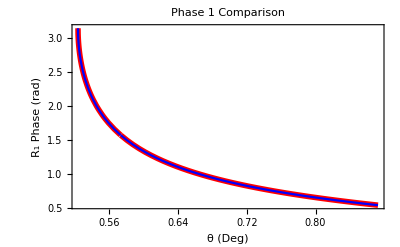

```mathematica
Plot[{Φ1[θ,1/2],Φ1$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_1 Phase (rad)",10]},PlotLabel->font["Phase 1 Comparison",14]]
```

Below is a comparison of the two expressions for Φ_2. They are clearly equivalent.

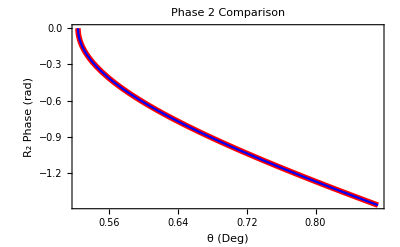

```mathematica
Plot[{Φ2[θ,1/2],Φ2$analytic[θ,1/2]},{θ,30 Degree, 50 Degree},PlotStyle->{{Thickness[.01],Red},Blue},Frame->True,FrameLabel->{font["θ (Deg)",10],font["R_2 Phase (rad)",10]},PlotLabel->font["Phase 2 Comparison",14]]
```

These formula can be used to calculate the GH shifts for each polarization using Artmann’s formulae:

```mathematica
Clear[GHshift$1,GHshift$2];
GHshift$1[θ_,n_]=1/k0 FullSimplify[D[Φ1$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]

GHshift$2[θ_,n_]=1/k0 FullSimplify[D[Φ2$analytic[θ,n],θ],1-n^2-Cos[θ]^2>0]
```

(4 n^2 Sin[θ])/(k0 (-1+n^2+(1+n^2) Cos[2 θ]) √(-n^2+Sin[θ]^2))

-(2 √2 Sin[θ])/(k0 √(1-2 n^2-Cos[2 θ]))

These are very small shifts in general. For instance, for 600 nm light and n = 0.5, the critical angle is 30°. At 35°, the GH shift for polarization 1 is only 600 nm. This is shown below.

```mathematica
Print["GH_1 for 600 nm light: ",GHshift$1[35. Degree,1/2]/. k0->2π/(600.0*10^-9)," meters"]
```

GH_1 for 600 nm light: -6.0434×10^-7 meters

Here is a plot of the GH shifts for both polarizations.

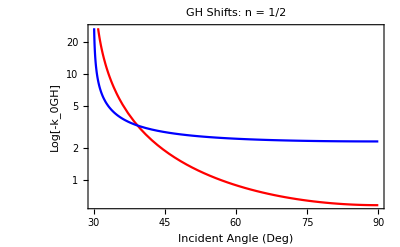

```mathematica
LogPlot[{-k0 GHshift$1[θ Degree,1/2],-k0 GHshift$2[θ Degree,1/2]},{θ,30 , 90 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-k_0GH]",12]},GridLines->Automatic]
```

Here is the same plot but now in units for 600 nm incident light.

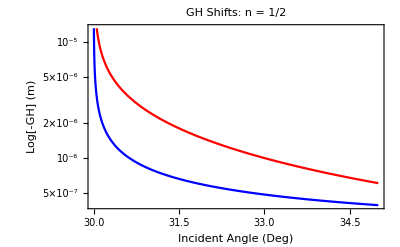

```mathematica
k0set = 2π/(600.*10^-9);

LogPlot[{-GHshift$1[θ Degree,1/2]/. k0->k0set,-GHshift$2[θ Degree,1/2]/. k0->k0set},{θ,30 , 35 },PlotStyle->{Red,Blue},Frame->True,PlotLabel->font["GH Shifts: n = 1/2",14],FrameLabel->{font["Incident Angle (Deg)",12],font["Log[-GH] (m)",12]},GridLines->Automatic]
```

## Applications

### Construction of E-field in Paraxial Approximation: Must Run Each Time

r … radial distance from the center axis of the beam

z … axial distance from the beam’s focus (or “waist”)

z_R… Rayleigh Range, π w0^2/λ

k = 2 π/λ  … wave number (in radians per meter) for a wavelength λ

E0 ≡ E(0,0) … electric field amplitude (and phase) at the origin at time 0

w(z) … radius at which the field amplitudes fall to 1/e of their axial values, at the plane z along the beam

w0 = w(0) … waist size

R(z) … radius of curvature of the beam’s wavefronts at z

ψ(z) … the Gouy phase at z, an extra phase term beyond that attributable to the phase velocity of light

p ... radial index ≥ 0

ℓ … azimuthal mode index ≥ 0

Nmax ... combined mode number, Nmax = |ℓ| + 2 p

There is also an understood time dependence e^(ⅈ ω t) multiplying such phasor quantities; the actual field at a point in time and space is given by the real part of that complex quantity.

```mathematica
Clear[Escalar,r,φfunc,z,w,w0,zR,λ,k,R,ψ,Nmax,Evec,k0];

ω = c1 k0;

r[x_,y_]=Sqrt[x^2+y^2];
φfunc[x_,y_]=ArcTan[x,y];

λ = 2 π/k0;

zR = π w0^2/λ;

w[z_]=w0 √(1+(z/zR)^2);

R[z_]=Simplify[z(1 + (zR/z)^2)];

Nmax = 2 p+Abs[ℓ];

ψ[z_]=(Nmax+1)ArcTan[zR,z];


Escalar[x_,y_,z_]=Simplify[1/w[z] Exp[(-(x^2+y^2))/w[z]^2]Exp[-ⅈ (k0 (x^2+y^2)/(2 R[z])+ k0 z+ψ[z])]((r[x,y] √2)/w[z])^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2(x^2+y^2))/w[z]^2]Exp[-ⅈ ℓ φfunc[x,y]],{Element[x,Reals],Element[y,Reals],Element[z,Reals]}];
```

```mathematica
Escalar2D[x_,y_]=FullSimplify[Escalar[x,y,0],{k0>0,w0>0}] /. w0 ->wk/k0
```

1/wk 2^(Abs[ℓ]/2) ⅇ^(-(k0^2 (x^2+y^2))/wk^2-ⅈ ℓ ArcTan[x,y]) k0 (k0/(wk √(1/(x^2+y^2))))^Abs[ℓ] LaguerreL[p,Abs[ℓ],(2 k0^2 (x^2+y^2))/wk^2]

### Key Fields: Must Run Each Time

```mathematica
Clear[κvec,κx,κy,κz];

κvec = {κx ,κy,√(1-κx^2-κy^2)};

κvec0 = {0,0,1};


nvec = {-Sin[θ],0,Cos[θ]};
```

### Fresnel Coefficients: Must Run Each Time

```mathematica
Clear[R1,R2,β,n];

β =ArcCos[κvec.nvec];

R2=(Cos[β]-√(n^2-Sin[β]^2))/(Cos[β]+√(n^2-Sin[β]^2)) ;  (* Fresnel Reflection Coefficient: s/TE *)

R1=(n^2 Cos[β]-√(n^2-Sin[β]^2))/(n^2 Cos[β]+√(n^2-Sin[β]^2));(* Fresnel Reflection Coefficient: p/TM *)

T2=Simplify[(2Cos[β])/(Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: s/TE *)

T1=Simplify[(2n Cos[β])/(n^2 Cos[β]+√(n^2-Sin[β]^2))];(* Fresnel Transmission Coefficient: p/TM *)
```

```mathematica
R1 /. {κx->0,κy->0}
```

(n^2 Cos[θ]-√(-1+n^2+Cos[θ]^2))/(n^2 Cos[θ]+√(-1+n^2+Cos[θ]^2))

```mathematica
θbrewster = ArcTan[n]
```

ArcTan[n]

```mathematica
Simplify[R1/. θ->θbrewster/. {κx->0,κy->0},{n>0}]

Simplify[R2/. θ->θbrewster/. {κx->0,κy->0},{n>0}]
```

0

(1-n^2)/(1+n^2)

```mathematica
θbrewster/Degree/. n->1.5168
```

56.6038

### Centroid Shift Imaging: 200 x 200 Domain

```mathematica
Clear[plots,k0];

fontset = 6;
fset = 1;

spinlabel=Which[fset ==1,"p/TM/1",fset ==2,"s/TE/2",fset ==3,"spin = +1",fset ==4,"spin = -1"]

λ0 = 2 π;
(* dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *) *)
dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

θloop = π/3.;


θloop =56.7 Degree;
θloop =60. Degree;
(* params$here = {wk->20.,n->1.5168,θ->θloop,k0->1,p->0,ℓ->6}; *)
params$here = {wk->20.,n->1.5168,θ->θloop,k0->1,p->0,ℓ->6};

nset = n /. params$here;

Print["Angle of Incidence: ",θloop/Degree,"°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, IFshift$R1={IFshift$Rx,IFshift$Ry},f$flag==2,IFshift$R2={IFshift$Rx,IFshift$Ry},f$flag==3,IFshift$R3={IFshift$Rx,IFshift$Ry},f$flag==4,IFshift$R4={IFshift$Rx,IFshift$Ry}];

Print[f$flag,": ",IFshift$Rx,", ",IFshift$Ry]

},{f$flag,fset,fset}];
```

p/TM/1

Angle of Incidence: 60.°

1: 0, -2.10277

```mathematica
ky$shift = 0.01Round[100Chop[Δx (NY$R-((dimset-1)/2+1))]]
```

-20.88

```mathematica
fontset =10;
domfac = 2.0;

SetDirectory[NotebookDirectory[]];
ERbeam$magsq$cpp = Import["crescents.tsv"];

maxval=Max[Re[Flatten[ERbeam$magsq]]];
maxval$cpp=Max[Flatten[ERbeam$magsq$cpp]];
ERbeam$magsq/maxval
ERbeam$magsq$cpp/maxval$cpp
```

{{3.32863×10^-29+0. ⅈ,3.33996×10^-29+0. ⅈ,3.3219×10^-29+0. ⅈ,3.2222×10^-29+0. ⅈ,3.15949×10^-29+0. ⅈ,191,3.10557×10^-29+0. ⅈ,3.21358×10^-29+0. ⅈ,3.2607×10^-29+0. ⅈ,3.29259×10^-29+0. ⅈ,3.35646×10^-29+0. ⅈ},199,{1}}
 |  |  |  |

{{0.00445358,0.0111112,0.00457724,0.0111038,0.00440861,0.011052,0.00435777,387,0.0108313,0.00434953,0.0109124,0.00441446,0.0110231,0.0044511,0.01097},399,{1}}
 |  |  |  |

```mathematica
p$R =ListDensityPlot[1/(1-0.0)(-0.0+(Chop[ERbeam$magsq/maxval])),PlotRange->{{domfac 85,domfac 116},{domfac 85,domfac 116},All},ColorFunction->GrayLevel,ColorFunctionScaling->False];
p$R$cpp =ListDensityPlot[1/(1-0.0)(-0.0+(Chop[ERbeam$magsq$cpp/maxval$cpp])),PlotRange->{{domfac 85,domfac 116},{domfac 85,domfac 116},All},ColorFunction->GrayLevel,ColorFunctionScaling->False];


p$line$vert=Graphics[{Green,Line[{{(dimset-1)/2+1,0},{(dimset-1)/2+1,dimset}}]}];

p$line$horiz=Graphics[{Green,Line[{{0,(dimset-1)/2+1},{dimset,(dimset-1)/2+1}}]}];

p$centroid=Show[Graphics[{Yellow,Disk[{NX$R,NY$R},.3]}],Frame->True];

p$pos$final=Show[p$R,p$line$vert,p$line$horiz,p$centroid,Graphics[{White,Text[font["L-G Reflection:",fontset],{domfac 95,domfac 110}]}],
Graphics[{Yellow,Text[font["Centroid",fontset],{domfac 95,domfac 109}]}],
Graphics[{White,Text[font["IF Shift: k y = "<>ToString[ky$shift],fontset],{domfac 95,domfac 108}]}],Graphics[{White,Text[font["ℓ="<>ToString[ℓ /. params$here]<>", "<>spinlabel<>", p="<>ToString[p /. params$here]<>"              n="<>ToString[0.1Round[10.0 n /. params$here]]<>", θ="<>ToString[0.1Round[10.θloop/Degree /. params$here]]<>"°",fontset],{domfac 101,domfac 91}]}],
FrameLabel->{font["k_0x/"<>ToString[Round[Δx]],fontset],font["k_0y/"<>ToString[Round[Δx]],fontset]}]

p$pos$final$cpp=Show[p$R$cpp,p$line$vert,p$line$horiz,p$centroid,Graphics[{White,Text[font["L-G Reflection:",fontset],{domfac 95,domfac 110}]}],
Graphics[{Yellow,Text[font["Centroid",fontset],{domfac 95,domfac 109}]}],
Graphics[{White,Text[font["IF Shift: k y = "<>ToString[ky$shift],fontset],{domfac 95,domfac 108}]}],Graphics[{White,Text[font["ℓ="<>ToString[ℓ /. params$here]<>", "<>spinlabel<>", p="<>ToString[p /. params$here]<>"              n="<>ToString[0.1Round[10.0 n /. params$here]]<>", θ="<>ToString[0.1Round[10.θloop/Degree /. params$here]]<>"°",fontset],{domfac 101,domfac 91}]}],
FrameLabel->{font["k_0x/"<>ToString[Round[Δx]],fontset],font["k_0y/"<>ToString[Round[Δx]],fontset]}]
```

-Graphics-

-Graphics-

```mathematica
ERtab$magsq = Table[Conjugate[ERtab[[i,j]]].ERtab[[i,j]],{i,1,dimset},{j,1,dimset}];

maxval=Max[Re[Flatten[ERtab$magsq]]];

p$Rκ =ListDensityPlot[Re[1/(1-0.0)(-0.0+(Chop[ERtab$magsq/maxval]))],ColorFunction->GrayLevel,ColorFunctionScaling->False,PlotRange->{{61,141},{61,141},All},FrameLabel->{"κy","κx"}]

p$line$vert=Graphics[{Green,Line[{{(dimset-1)/2+1,0},{(dimset-1)/2+1,dimset}}]}];

p$line$horiz=Graphics[{Green,Line[{{0,(dimset-1)/2+1},{dimset,(dimset-1)/2+1}}]}];
p$freq$final=Show[p$Rκ,p$line$vert,p$line$horiz,Graphics[{White,Text[font["L-G Reflection:",fontset],{84,128}]}],Graphics[{White,Text[font["K-space",fontset],{84,125}]}],Graphics[{White,Text[font["ℓ="<>ToString[ℓ /. params$here]<>", "<>spinlabel<>", p="<>ToString[p /. params$here]<>"              n="<>ToString[0.1Round[10.0nset /. params$here]]<>", θ="<>ToString[0.1Round[10.θ/Degree /. params$here]]<>"°",fontset],{100,70}]}],FrameLabel->{font["κ_x",14],font["κ_y",fontset]}]
```

-Graphics-

-Graphics-

```mathematica
GraphicsRow[{p$freq$final,p$pos$final},ImageSize->700]
```

-Graphics-

### Centroid Shift Imaging: 400 x 400 Domain

```mathematica
Clear[plots,k0];

fontset = 6;
fset = 1;

spinlabel=Which[fset ==1,"p/TM/1",fset ==2,"s/TE/2",fset ==3,"spin = +1",fset ==4,"spin = -1"]

λ0 = 2 π;
(*
dimset = 201;kmax = 0.25; xmax =400000; (* w0 = 20000/k0 *)
dimset = 201;kmax = 0.25; xmax =400; (* w0 = 20/k0 *)
*)
dimset = 401;kmax = 0.25; xmax =400; (* w0 = 20/k0 *) (* for pretty pictures *)

small = π*10^-10;


Δx = (2.xmax)/(dimset-1);

Δκ = (2. π)/(2xmax k0)/. k0->1;

κperp[j_]=(2. π)/(2xmax k0)(j-(dimset+1)/2)/. k0->1;


rperp[n_]=2 xmax(n-(dimset+1)/2)/(dimset+1);

κtab= Table[{κperp[i],κperp[j],√(1-(κperp[i]^2+κperp[j]^2))},{j,1,dimset},{i,1,dimset}];

θloop = π/3.;


θloop =56.7 Degree;
θloop =60. Degree;
params$here = {wk->20.,n->1.5168,θ->θloop,k0->1,p->0,ℓ->6};

nset = n /. params$here;

Print["Angle of Incidence: ",θloop/Degree,"°"];

Etab = Table[Escalar2D[x,y]/.params$here ,{y,-xmax+small,xmax+small,Δx},{x,-xmax+small,xmax+small,Δx}];
E$tilde = RotateLeft[Fourier[Etab],{(dimset+1)/2,(dimset+1)/2}];
Do[If[κperp[i]^2+κperp[j]^2≥1,E$tilde[[i,j]]=0.0],{j,1,dimset},{i,1,dimset}]; (* Throws out evanescent incident kvecs *)

Do[{

f = Which[f$flag ==1,{1,0,0},f$flag==2,{0,1,0},f$flag==3,{1,ⅈ,0},f$flag==4,{1,-ⅈ,0}];

θR=π-θ /. params$here;

eR = {(f[[1]]R1-f[[2]]κy Cot[θ](R1+R2)),f[[2]]R2 + f[[1]]κy Cot[θ](R1+R2 ),-(f[[1]]R1 κx + f[[2]]R2  κy)} /. params$here;

eRtab = Table[eR /. {κx->κtab[[i,j]][[1]],κy->κtab[[i,j]][[2]]}/. params$here,{i,1,dimset},{j,1,dimset}];

ERtab=Table[E$tilde[[i,j]] eRtab[[i,j]]/. params$here,{i,1,dimset},{j,1,dimset}]; 

ERbeamtab =InverseFourier[ERtab];

ERbeam$magsq = Table[Conjugate[ERbeamtab[[i,j]]].ERbeamtab[[i,j]],{i,1,dimset},{j,1,dimset}]; 

NX$R=Sum[jx ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

NY$R=Sum[jy ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}]/Sum[ERbeam$magsq[[jy,jx]],{jx,1,dimset},{jy,1,dimset}];

IFshift$Rx =Chop[(Δx(NX$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

IFshift$Ry =Chop[(Δx(NY$R-(dimset+1)/2))/(2π/(632.8*10^-9))*10^6];

Which[f$flag ==1, IFshift$R1={IFshift$Rx,IFshift$Ry},f$flag==2,IFshift$R2={IFshift$Rx,IFshift$Ry},f$flag==3,IFshift$R3={IFshift$Rx,IFshift$Ry},f$flag==4,IFshift$R4={IFshift$Rx,IFshift$Ry}];

Print[f$flag,": ",IFshift$Rx,", ",IFshift$Ry]

},{f$flag,fset,fset}];
```

p/TM/1

Angle of Incidence: 60.°

1: 0, -2.10294

```mathematica
ky$shift = 0.01Round[100Chop[Δx (NY$R-((dimset-1)/2+1))]]
```

-20.88

```mathematica
fontset =10;
domfac = 2.0;

SetDirectory[NotebookDirectory[]];
ERbeam$magsq$cpp = Import["crescents.tsv"];

maxval=Max[Re[Flatten[ERbeam$magsq]]];
maxval$cpp=Max[Flatten[ERbeam$magsq$cpp]];
ERbeam$magsq/maxval;
ERbeam$magsq$cpp/maxval$cpp;
```

```mathematica
p$R =ListDensityPlot[Chop[ERbeam$magsq/maxval],PlotRange->{{domfac 85,domfac 116},{domfac 85,domfac 116},All},ColorFunction->GrayLevel,ColorFunctionScaling->False];
p$R$cpp =ListDensityPlot[Chop[ERbeam$magsq$cpp/maxval$cpp],PlotRange->{{domfac 85,domfac 116},{domfac 85,domfac 116},All},ColorFunction->GrayLevel,ColorFunctionScaling->False]

p$line$vert=Graphics[{Green,Line[{{(dimset-1)/2+1,0},{(dimset-1)/2+1,dimset}}]}];

p$line$horiz=Graphics[{Green,Line[{{0,(dimset-1)/2+1},{dimset,(dimset-1)/2+1}}]}];

p$centroid=Show[Graphics[{Yellow,Disk[{NX$R,NY$R},.3]}],Frame->True];

p$pos$final=Show[p$R,p$line$vert,p$line$horiz,p$centroid,Graphics[{White,Text[font["L-G Reflection:",fontset],{domfac 95,domfac 110}]}],
Graphics[{Yellow,Text[font["Centroid",fontset],{domfac 95,domfac 109}]}],
Graphics[{White,Text[font["IF Shift: k y = "<>ToString[ky$shift],fontset],{domfac 95,domfac 108}]}],Graphics[{White,Text[font["ℓ="<>ToString[ℓ /. params$here]<>", "<>spinlabel<>", p="<>ToString[p /. params$here]<>"              n="<>ToString[0.1Round[10.0 n /. params$here]]<>", θ="<>ToString[0.1Round[10.θloop/Degree /. params$here]]<>"°",fontset],{domfac 101,domfac 91}]}],
FrameLabel->{font["k_0x/"<>ToString[Round[Δx]],fontset],font["k_0y/"<>ToString[Round[Δx]],fontset]}]
```

-Graphics-

-Graphics-

```mathematica
ERtab$magsq = Table[Conjugate[ERtab[[i,j]]].ERtab[[i,j]],{i,1,dimset},{j,1,dimset}];

maxval=Max[Re[Flatten[ERtab$magsq]]];

p$Rκ =ListDensityPlot[Re[Chop[ERtab$magsq/maxval]],ColorFunction->GrayLevel,ColorFunctionScaling->False,PlotRange->{{160,250},{160,250}},FrameLabel->{"κy","κx"}];

p$line$vert=Graphics[{Green,Line[{{(dimset-1)/2+1,0},{(dimset-1)/2+1,dimset}}]}];

p$line$horiz=Graphics[{Green,Line[{{0,(dimset-1)/2+1},{dimset,(dimset-1)/2+1}}]}];
p$freq$final=Show[p$Rκ,p$line$vert,p$line$horiz,Graphics[{White,Text[font["L-G Reflection:",fontset],{180,245}]}],Graphics[{White,Text[font["K-space",fontset],{180,240}]}],Graphics[{White,Text[font["ℓ="<>ToString[ℓ /. params$here]<>", "<>spinlabel<>", p="<>ToString[p /. params$here]<>" n="<>ToString[0.1Round[10.0nset /. params$here]]<>", θ="<>ToString[0.1Round[10.θ/Degree /. params$here]]<>"°",fontset],{190,235}]}],FrameLabel->{font["κ_x",14],font["κ_y",fontset]}]
```

-Graphics-

```mathematica
GraphicsRow[{p$freq$final,p$pos$final},ImageSize->700]
```

-Graphics-